```mathematica
(*Load the packages*)
<<PhysicalConstants`;
<<Units`;

(*Define physical constants*)
alpha=FineStructureConstant;
c=SpeedOfLight//First;
eAu=ElectronCharge//First;
fPi=QuantityMagnitude[UnitConvert[Quantity[93, "MeV"], "eV"]];
gE=ElectronGFactor;
gP=ParticleData["Proton", "GFactor"];
h=PlanckConstant//First;
hbar=QuantityMagnitude[Quantity[1,"ReducedPlanckConstant"],"J*s"];
MSolar=QuantityMagnitude[Quantity[1, "SolarMass"], "Kilograms"];
mPl=PlanckMass//First;
mPi=QuantityMagnitude[UnitConvert[ParticleData["PiZero","Mass"], "eV/c^2"]];
muB=QuantityMagnitude[Quantity[1,"BohrMagneton"],"J/T"];
rE=BohrRadius//First;

(*Conversion factors*)
CToEv=(4*Pi*alpha)^(1/2)/eAu;
kgToEv=c^2/eAu;
mToEvMinus1=eAu/hbar/c;
JToEv=1/eAu;
pcToM=QuantityMagnitude[Quantity[1, "Parsecs"], "Meters"];
sToEvMinus1=eAu/(hbar);
TToEv2=kgToEv/CToEv/sToEvMinus1;
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*Common parameters*)
BbarValT=10^-10;(*Background magnetic field (T)*)
BbarVal=BbarValT*TToEv2;(*Background magnetic field (eV^2)*)
BbarXVal=BbarVal;
BbarYVal=BbarVal;
BbarZVal=BbarVal;
rPVal=8000*pcToM*mToEvMinus1;(*Calculate distance of L1544 from Galactic Centre (eV^-1)*)

(*Parameters of flat potential*)
f=1*10^26; (*Energy scale of axion (eV)*)
mA=1*10^-22; (*Axion mass, 1e-18 to 1e-22 (eV)*)
mD=1*10^-22; (*Dark photon mass, 1e-18 to 1e-22 (eV)*)
mU=1*10^-6*mD; (*Chemical potential of dark photon (eV)*)
rCPc=180; (*Core radius (pc)*)

(*Calculate mass density of axion field (eV^4)*)
rho0=1.9*(mA/10^-23)^(-2)*(rCPc/10^3)^(-4)*MSolar;
rho0*=kgToEv*(pcToM*mToEvMinus1)^(-3);

(*Scaling constants*)
aA=(9.1*10^-2/rCPc^2)*(pcToM*mToEvMinus1)^(-2); (*Scaling constant of axion (eV^2)*)
aD=aA; (*Scaling constant of dark photon (eV^2)*)

(*Core radius (eV^-1)*)
rCVal=rCPc*pcToM*mToEvMinus1;
CutoffFactor=Sqrt[(2^(1/4)-1)/(9.1*10^-2)];

(*Calculate amplitudes*)
phi0=Sqrt[2*rho0]/mA; (*Amplitude of axion potential (eV)*)
A0=phi0; (*Amplitude of dark photon potential (eV)*)

(*Coupling constants and frequencies*)
gAc=alpha/Pi/f ;(*Coupling constant (eV^-1)*)
epsilon=1*10^-3; (*Coupling strength, 1e-3 to 1e-5*)
omegaA=mA; (*Oscillation frequency of axion (eV)*)
omegaD=mD-mU; (*Oscillation frequency of dark photon (eV)*)

(*Calculate the proportionality constant between dark photon and axion*)
Print["Proportionality constant between dark photon and axion: ", epsilon*mD/(gAc*BbarVal)]
```

Proportionality constant between dark photon and axion: 2.20376×10^11

```mathematica
(*Define the profile*)
fProfile[x_, y_, z_]:=1/((1+a*(x^2+y^2+z^2))^4);
Print["f: ",fProfile[x,y,z]];

(*Define the magnetic field*)
BbarP={BbarXP, BbarYP, BbarZP};
fvec[x_, y_, z_]:=BbarP*fProfile[x, y, z];
Print["fvec: ", fvec[x, y, z]]
```

f: 1/((1+a (x^2+y^2+z^2))^4)

fvec: {BbarXP/((1+a (x^2+y^2+z^2))^4),BbarYP/((1+a (x^2+y^2+z^2))^4),BbarZP/((1+a (x^2+y^2+z^2))^4)}

```mathematica
(*Calculate the curl of vector field*)
curlfvec=Curl[fvec[x, y, z], {x, y, z}]//FullSimplify
```

{(a (-8 BbarZP y+8 BbarYP z))/((1+a (x^2+y^2+z^2))^5),(8 a (BbarZP x-BbarXP z))/((1+a (x^2+y^2+z^2))^5),(a (-8 BbarYP x+8 BbarXP y))/((1+a (x^2+y^2+z^2))^5)}

```mathematica
(*Define the inner inner integrand*)
curlfvec=curlfvec/.{x->r*Sin[θ]*Cos[ϕ], y->r*Sin[θ]*Sin[ϕ], z->r*Cos[θ]}//FullSimplify
getA[δ_]:=3^(11+δ)*a^(3/2+δ/2)*Exp[2+δ]/12500;
curlfvec=curlfvec/(8a*r/(1+a*r^2)^5)*getA[δ]*r^(2+δ)*Exp[-3*(2+δ)*Sqrt[a]*r]/.δ->0
curlfvecInInInt=1/(4*Pi*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]])*r^2*Sin[θ]*curlfvec*Exp[-I*ω*t]*Exp[I*ω*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]]]//FullSimplify
```

{(8 a r (BbarYP Cos[θ]-BbarZP Sin[θ] Sin[ϕ]))/((1+a r^2)^5),(8 a r (-BbarXP Cos[θ]+BbarZP Cos[ϕ] Sin[θ]))/((1+a r^2)^5),(8 a r Sin[θ] (-BbarYP Cos[ϕ]+BbarXP Sin[ϕ]))/((1+a r^2)^5)}

{(177147 a^(3/2) ⅇ^(2-6 √a r) r^2 (BbarYP Cos[θ]-BbarZP Sin[θ] Sin[ϕ]))/12500,(177147 a^(3/2) ⅇ^(2-6 √a r) r^2 (-BbarXP Cos[θ]+BbarZP Cos[ϕ] Sin[θ]))/12500,(177147 a^(3/2) ⅇ^(2-6 √a r) r^2 Sin[θ] (-BbarYP Cos[ϕ]+BbarXP Sin[ϕ]))/12500}

{(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^4 Sin[θ] (BbarYP Cos[θ]-BbarZP Sin[θ] Sin[ϕ]))/(50000 π √(r^2+rP^2-2 r rP Cos[θ])),(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^4 Sin[θ] (-BbarXP Cos[θ]+BbarZP Cos[ϕ] Sin[θ]))/(50000 π √(r^2+rP^2-2 r rP Cos[θ])),-(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^4 Sin[θ]^2 (BbarYP Cos[ϕ]-BbarXP Sin[ϕ]))/(50000 π √(r^2+rP^2-2 r rP Cos[θ]))}

```mathematica
(*Integrate along ϕ from 0 to 2π*)
curlfvecInInt={Integrate[curlfvecInInInt[[1]],{ϕ,0,2*Pi}],Integrate[curlfvecInInInt[[2]],{ϕ,0,2*Pi}],Integrate[curlfvecInInInt[[3]],{ϕ,0,2*Pi}]}//FullSimplify
```

{(177147 a^(3/2) BbarYP ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^4 Sin[2 θ])/(50000 √(r^2+rP^2-2 r rP Cos[θ])),-(177147 a^(3/2) BbarXP ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^4 Sin[2 θ])/(50000 √(r^2+rP^2-2 r rP Cos[θ])),0}

```mathematica
(*x component with field replacement*)
curlfvecInIntX=curlfvecInInt[[1]];
curlfvecInIntY=curlfvecInInt[[2]];
curlfvecInIntXRep=curlfvecInIntX/.{BbarYP->-BbarXP};
curlfvecInIntXRep-curlfvecInIntY//FullSimplify
```

0

```mathematica
(*Integrate along θ from 0 to π*)
curlfvecIntX=Assuming[ω>0&&r>0&&rP>0, Integrate[curlfvecInIntX, θ]]
curlfvecIntXPi=curlfvecIntX/.{θ->Pi};
curlfvecIntX0=curlfvecIntX/.{θ->0};
curlfvecIntXDiff=curlfvecIntXPi-curlfvecIntX0;
curlfvecIntXrPBig=FullSimplify[curlfvecIntXDiff, {r>0, rP>0, rP>r}];
curlfvecIntXrBig=FullSimplify[curlfvecIntXDiff, {r>0, rP>0, r>rP}];
Print["Integrand when rP>r: ", curlfvecIntXrPBig]
Print["Integrand when r>rP: ", curlfvecIntXrBig]
```

-(177147 a^(3/2) BbarYP ⅇ^2 r^2 (ⅈ+ⅈ r rP ω^2 Cos[θ]+ω √(r^2+rP^2-2 r rP Cos[θ])) (Cosh[6 √a r+ⅈ ω (t-√(r^2+rP^2-2 r rP Cos[θ]))]-Sinh[6 √a r+ⅈ ω (t-√(r^2+rP^2-2 r rP Cos[θ]))]))/(25000 rP^2 ω^3)

Integrand when rP>r: (177147 ⅈ a^(3/2) BbarYP ⅇ^(2-6 √a r+ⅈ (rP-t) ω) r^2 (ⅈ+rP ω) (r ω Cos[r ω]-Sin[r ω]))/(12500 rP^2 ω^3)

Integrand when r>rP: (177147 ⅈ a^(3/2) BbarYP ⅇ^(2-6 √a r+ⅈ (r-t) ω) r^2 (ⅈ+r ω) (rP ω Cos[rP ω]-Sin[rP ω]))/(12500 rP^2 ω^3)

```mathematica
(*Integrate along r*)
curlfvecIXrPBig=Integrate[curlfvecIntXrPBig, r];
curlfvecIXrBig=Integrate[curlfvecIntXrBig, r];
Print["Integral when rP>r: ", curlfvecIXrPBig]
Print["Integral when r>rP: ", curlfvecIXrBig]
```

Integral when rP>r: 1/(12500 rP^2 ω^3 (36 a+ω^2)^4)177147 ⅈ a^(3/2) BbarYP ⅇ^(2-6 √a r+ⅈ (rP-t) ω) (ⅈ+rP ω) (-2 ω (46656 a^3 r^2+139968 a^(7/2) r^3+4 ω^4-2 r^2 ω^6+3 √a r ω^4 (-22+r^2 ω^2)+108 a^(3/2) r ω^2 (-20+3 r^2 ω^2)+3888 a^(5/2) r (2+3 r^2 ω^2)-36 a ω^2 (20+3 r^2 ω^2)) Cos[r ω]+(279936 a^(7/2) r^2+r ω^6 (-8+r^2 ω^2)+46656 a^3 r (2+r^2 ω^2)+1080 a^(3/2) ω^2 (4+3 r^2 ω^2)+36 a r ω^4 (10+3 r^2 ω^2)+1296 a^2 r ω^2 (20+3 r^2 ω^2)+6 √a ω^4 (-30+7 r^2 ω^2)+7776 a^(5/2) (2+9 r^2 ω^2)) Sin[r ω])

Integral when r>rP: -(177147 ⅈ a^(3/2) BbarYP ⅇ^(2-6 √a r+ⅈ r ω-ⅈ t ω) (216 a^(3/2) r^2 (ⅈ+r ω)+36 a r (2 ⅈ+6 r ω-3 ⅈ r^2 ω^2)+ω (8-8 ⅈ r ω-4 r^2 ω^2+ⅈ r^3 ω^3)-6 √a (-2 ⅈ-10 r ω+9 ⅈ r^2 ω^2+3 r^3 ω^3)) (rP ω Cos[rP ω]-Sin[rP ω]))/(12500 rP^2 (6 √a-ⅈ ω)^4 ω^3)

```mathematica
(*Substitute r=0 to the integral*)
curlfvecI0=curlfvecIXrPBig/.r->0;
Print["Value of the integral at r=0: ", curlfvecI0]
```

Value of the integral at r=0: -(177147 ⅈ a^(3/2) BbarYP ⅇ^(2+ⅈ (rP-t) ω) (ⅈ+rP ω) (-720 a ω^2+4 ω^4))/(6250 rP^2 ω^2 (36 a+ω^2)^4)

```mathematica
(*Substitute r=Infinity to the integral*)
curlfvecIInf=Assuming[ω>0,Limit[curlfvecIXrBig,r->Infinity]]//FullSimplify;
Print["Expression of the integral at r=Infinity: ", curlfvecIInf]
curlfvecIInfVal=curlfvecIInf/.{a->aA, rC->rCVal, rP->rPVal, BbarYP->BbarYVal, ω->omegaA, t->0};
Print["Value of the integral at r=Infinity: ", curlfvecIInfVal]
```

Expression of the integral at r=Infinity: 0

Value of the integral at r=Infinity: 0

```mathematica
(*Substitute r=rP to the integral*)
curlfvecIXrPrPBig=curlfvecIXrPBig/.{r->rP};
curlfvecIXrPrBig=curlfvecIXrBig/.{r->rP};
curlfvecIXrP=-curlfvecIXrPrBig+curlfvecIXrPrPBig//FullSimplify;
Print["Expression of the integral at r=rP: ", curlfvecIXrP]
curlfvecIXrPVal=curlfvecIXrP/.{a->aA, rC->rCVal,rP->rPVal, BbarYP->BbarYVal, ω->omegaA, t->0};
Print["Value of the integral at r=rP: ", curlfvecIXrPVal]
```

Expression of the integral at r=rP: -(177147 a^(3/2) BbarYP ⅇ^(2-6 √a rP-ⅈ t ω) (288 a (5+30 √a rP+18 a rP^2 (5+9 √a rP+9 a rP^2))+8 (-1-6 √a rP+18 a rP^2 (4+18 √a rP+27 a rP^2)) ω^2+4 rP^2 (-1+9 √a rP+27 a rP^2) ω^4+rP^4 ω^6))/(12500 rP^2 (36 a+ω^2)^4)

Value of the integral at r=rP: -4.56612×10^-21

```mathematica
(*Substitute r=10rc to the integral*)
curlfvecIX10rcA=curlfvecIXrPBig/.{r->10*rCVal, a->aA, rC->rCVal, rP->rPVal, BbarYP->BbarYVal, ω->omegaA, t->0};
curlfvecIX10rcD=curlfvecIXrPBig/.{r->10*rCVal, a->aD, rC->rCVal, rP->rPVal, BbarYP->1/Sqrt[2]*I, ω->omegaD, t->0};
Print["Value of the integral at r=10rc for axion: ", curlfvecIX10rcA]
Print["Value of the integral at r=10rc for dark photon: ", curlfvecIX10rcD]
```

Value of the integral at r=10rc for axion: 45009.8-40871.8 ⅈ

Value of the integral at r=10rc for dark photon: 1.67937×10^12+1.43893×10^12 ⅈ

```mathematica
(*Expression of the integral*)
curlfvecI=curlfvecIInf+curlfvecIXrP-curlfvecI0//FullSimplify;
Print["Expression of the integral: ", curlfvecI]
curlfvecI/.{t->0, ω->m}
```

Expression of the integral: 1/(12500 rP^2 (36 a+ω^2)^4)177147 a^(3/2) BbarYP ⅇ^2 (8 ⅈ ⅇ^(ⅈ (rP-t) ω) (ⅈ+rP ω) (-180 a+ω^2)-ⅇ^(-6 √a rP-ⅈ t ω) (288 a (5+30 √a rP+18 a rP^2 (5+9 √a rP+9 a rP^2))+8 (-1-6 √a rP+18 a rP^2 (4+18 √a rP+27 a rP^2)) ω^2+4 rP^2 (-1+9 √a rP+27 a rP^2) ω^4+rP^4 ω^6))

1/(12500 (36 a+m^2)^4 rP^2)177147 a^(3/2) BbarYP ⅇ^2 (8 ⅈ ⅇ^(ⅈ m rP) (-180 a+m^2) (ⅈ+m rP)-ⅇ^(-6 √a rP) (m^6 rP^4+4 m^4 rP^2 (-1+9 √a rP+27 a rP^2)+288 a (5+30 √a rP+18 a rP^2 (5+9 √a rP+9 a rP^2))+8 m^2 (-1-6 √a rP+18 a rP^2 (4+18 √a rP+27 a rP^2))))

```mathematica
ϵ*m^2*Sqrt[2*ρ]/m*Assuming[rC>0,(354294 ⅈ a^(3/2) BbarYP ⅇ^(2+ⅈ m rP))/(3125 m^5 rP)/.a->0.091/rC^2//FullSimplify]
mD*rCVal
```

((0.+4.4014 ⅈ) BbarYP ⅇ^(2+ⅈ m rP) ϵ √ρ)/(m^4 rC^3 rP)

2814.73

```mathematica
(*Calculate the magnetic field*)
B1A=omegaA*gAc*phi0*curlfvecI/.{a->aA, rC->rCVal, rP->rPVal, BbarYP->BbarYVal, ω->omegaA, t->0};
B1D=epsilon*mD^2*A0*curlfvecI/.{ a->aD, rC->rCVal, rP->rPVal, BbarYP->1/Sqrt[2]*I, ω->omegaD, t->0};
B1AT=B1A/TToEv2;
B1DT=B1D/TToEv2;
Print["Magnetic field induced by axion (T): ", B1AT, ", (G): ",B1AT*10^4]
Print["Magnetic field induced by dark photon (T): ", B1DT, ", (G): ", B1DT*10^4]
```

Magnetic field induced by axion (T): -1.45664×10^-32+1.32272×10^-32 ⅈ, (G): -1.45664×10^-28+1.32272×10^-28 ⅈ

Magnetic field induced by dark photon (T): -2.32831×10^-21-1.99496×10^-21 ⅈ, (G): -2.32831×10^-17-1.99496×10^-17 ⅈ

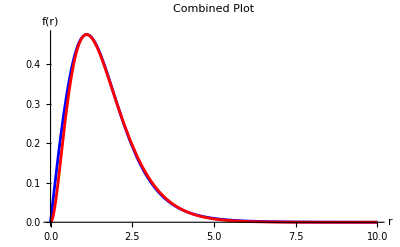

```mathematica
(*Define the plots of curl of current*)
plotcurlfvec=Plot[8*0.091*r/(1+0.091*r^2)^5,{r,0,10},PlotRange->All,PlotStyle->Blue,PlotLabel->"Combined Plot",AxesLabel->{"r","f(r)"}];
plotcurlfvecFit=Plot[getA[δ]*r^(2+δ)*Exp[-3*(2+δ)*Sqrt[a]*r]/.{δ->0, a->0.091},{r,0,10},PlotRange->All,PlotStyle->Red];
(*Combine the plots*)
Show[plotcurlfvec, plotcurlfvecFit]
```

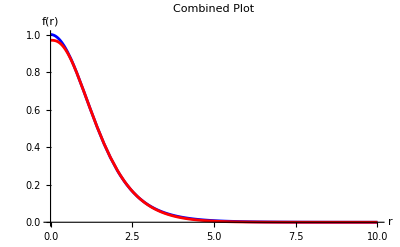

```mathematica
(*Define the plots of profile*)
plotcurlfProfile=Plot[1/(1+0.091*r^2)^4,{r,0,10},PlotRange->All,PlotStyle->Blue,PlotLabel->"Combined Plot",AxesLabel->{"r","f(r)"}];
plotcurlfProfileFit=Plot[6561/100000*Exp[2]*Gamma[3, 6*Sqrt[0.091]*r],{r,0,10},PlotRange->All,PlotStyle->Red];
(*Combine the plots*)
Show[plotcurlfProfile,plotcurlfProfileFit]
```

```mathematica
(*Define the approximate vector field*)
fProfileApx[x_, y_, z_]:=1*HeavisideTheta[(rCutoff-Sqrt[x^2+y^2+z^2])]
Print["Approximate f: ",fProfileApx[x,y,z]]
fvecApx[x_, y_, z_]:=BbarP*fProfileApx[x, y, z];
Print["fvecApx: ", fvecApx[x, y, z]]
```

Approximate f: HeavisideTheta[rCutoff-√(x^2+y^2+z^2)]

fvecApx: {BbarXP HeavisideTheta[rCutoff-√(x^2+y^2+z^2)],BbarYP HeavisideTheta[rCutoff-√(x^2+y^2+z^2)],BbarZP HeavisideTheta[rCutoff-√(x^2+y^2+z^2)]}

```mathematica
(*Calculate the curl of the approximate vector field*)
curlfvecApx=Curl[fvecApx[x, y, z], {x, y, z}]//FullSimplify
```

{-(BbarZP y DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))+(BbarYP z DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2)),(BbarZP x DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))-(BbarXP z DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2)),-(BbarYP x DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))+(BbarXP y DiracDelta[rCutoff-√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))}

```mathematica
(*Define the inner inner integrand*)
curlfvecApx=Assuming[r>0, FullSimplify[curlfvecApx/.{x->r*Sin[θ]*Cos[ϕ], y->r*Sin[θ]*Sin[ϕ], z->r*Cos[θ]}]]
curlfvecInInIntApx=1/(4*Pi*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]])*r^2*Sin[θ]*Exp[-I*ω*t]*Exp[I*ω*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]]]*curlfvecApx//FullSimplify
```

{BbarYP Cos[θ] DiracDelta[-r+rCutoff]-BbarZP DiracDelta[-r+rCutoff] Sin[θ] Sin[ϕ],-BbarXP Cos[θ] DiracDelta[-r+rCutoff]+BbarZP Cos[ϕ] DiracDelta[-r+rCutoff] Sin[θ],-BbarYP Cos[ϕ] DiracDelta[-r+rCutoff] Sin[θ]+BbarXP DiracDelta[-r+rCutoff] Sin[θ] Sin[ϕ]}

{(ⅇ^(ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 Sin[θ] (BbarYP Cos[θ] DiracDelta[-r+rCutoff]-BbarZP DiracDelta[-r+rCutoff] Sin[θ] Sin[ϕ]))/(4 π √(r^2+rP^2-2 r rP Cos[θ])),(ⅇ^(ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 Sin[θ] (-BbarXP Cos[θ] DiracDelta[-r+rCutoff]+BbarZP Cos[ϕ] DiracDelta[-r+rCutoff] Sin[θ]))/(4 π √(r^2+rP^2-2 r rP Cos[θ])),(ⅇ^(ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 Sin[θ] (-BbarYP Cos[ϕ] DiracDelta[-r+rCutoff] Sin[θ]+BbarXP DiracDelta[-r+rCutoff] Sin[θ] Sin[ϕ]))/(4 π √(r^2+rP^2-2 r rP Cos[θ]))}

```mathematica
(*Integrate along ϕ from 0 to 2π*)
curlfvecInIntApx={Integrate[curlfvecInInIntApx[[1]],{ϕ,0,2*Pi}],Integrate[curlfvecInInIntApx[[2]],{ϕ,0,2*Pi}],Integrate[curlfvecInInIntApx[[3]],{ϕ,0,2*Pi}]}//FullSimplify
```

{(BbarYP ⅇ^(ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 Cos[θ] DiracDelta[-r+rCutoff] Sin[θ])/(2 √(r^2+rP^2-2 r rP Cos[θ])),-(BbarXP ⅇ^(ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 Cos[θ] DiracDelta[-r+rCutoff] Sin[θ])/(2 √(r^2+rP^2-2 r rP Cos[θ])),0}

```mathematica
(*x component with field replacement*)
curlfvecInIntXApx=curlfvecInIntApx[[1]];
curlfvecInIntYApx=curlfvecInIntApx[[2]];
curlfvecInIntXRepApx=curlfvecInIntXApx/.{BbarYP->-BbarXP};
curlfvecInIntYApx-curlfvecInIntXRepApx//FullSimplify
```

0

```mathematica
(*Integrate along θ from 0 to π*)
curlfvecIntXApx=Assuming[ω>0&&t>0&&r>0&&rP>0&&rCutoff>0, Integrate[curlfvecInIntXApx, θ]];
curlfvecIntXPiApx=curlfvecIntXApx/.{θ->Pi};
curlfvecIntX0Apx=curlfvecIntXApx/.{θ->0};
curlfvecIntXDiffApx=curlfvecIntXPiApx-curlfvecIntX0Apx;
curlfvecIntXrPBigApx=Simplify[curlfvecIntXDiffApx, {r>0, rP>0, rP>r}];
curlfvecIntXrBigApx=Simplify[curlfvecIntXDiffApx, {r>0, rP>0, r>rP}];
Print["Approximate integrand when rP>r: ", curlfvecIntXrPBigApx]
Print["Approximate integrand when r>rP: ", curlfvecIntXrBigApx]
```

Approximate integrand when rP>r: (BbarYP ⅇ^(-ⅈ (r-rP+t) ω) (1+ⅈ r ω) (ⅈ+rP ω) DiracDelta[-r+rCutoff])/(2 rP^2 ω^3)+(ⅈ BbarYP ⅇ^(ⅈ (r+rP-t) ω) (ⅈ+r ω) (ⅈ+rP ω) DiracDelta[-r+rCutoff])/(2 rP^2 ω^3)

Approximate integrand when r>rP: (BbarYP ⅇ^(ⅈ (r-rP-t) ω) (ⅈ+r ω) (1+ⅈ rP ω) DiracDelta[-r+rCutoff])/(2 rP^2 ω^3)+(ⅈ BbarYP ⅇ^(ⅈ (r+rP-t) ω) (ⅈ+r ω) (ⅈ+rP ω) DiracDelta[-r+rCutoff])/(2 rP^2 ω^3)

```mathematica
(*Integrate along r*)
curlfvecIrPBigOutApx=curlfvecIntXrPBigApx/.{DiracDelta[-r+rCutoff]->1, r->rCutoff}//FullSimplify;
curlfvecIrBigOutApx=0;
curlfvecIrPBigInApx=0;
curlfvecIrBigInApx=curlfvecIntXrBigApx/.{DiracDelta[-r+rCutoff]->1, r->rCutoff}//FullSimplify;
Print["Approximate integral when rP>r and rP>rCutoff: ", curlfvecIrPBigOutApx]
Print["Approximate integral when r>rP>rCutoff: ",curlfvecIrBigOutApx]
Print["Approximate integral when rCutoff>rP>r: ", curlfvecIrPBigInApx]
Print["Approximate integral when r>rP and rCutoff>rP: ", curlfvecIrBigInApx]
```

Approximate integral when rP>r and rP>rCutoff: (BbarYP ⅇ^(ⅈ (rP-t) ω) (-1+ⅈ rP ω) (rCutoff ω Cos[rCutoff ω]-Sin[rCutoff ω]))/(rP^2 ω^3)

Approximate integral when r>rP>rCutoff: 0

Approximate integral when rCutoff>rP>r: 0

Approximate integral when r>rP and rCutoff>rP: (BbarYP ⅇ^(ⅈ (rCutoff-t) ω) (-1+ⅈ rCutoff ω) (rP ω Cos[rP ω]-Sin[rP ω]))/(rP^2 ω^3)

```mathematica
(*Expression of the approximate integral*)
curlfvecIOutApx=curlfvecIrPBigOutApx+curlfvecIrBigOutApx//FullSimplify;
curlfvecIInApx=curlfvecIrPBigInApx+curlfvecIrBigInApx//FullSimplify;
Print["Approximate integral when rP>rCutOff: ", curlfvecIOutApx] 
Print["Approximate integral when rCutOff>rP: ", curlfvecIInApx]
```

Approximate integral when rP>rCutOff: (BbarYP ⅇ^(ⅈ (rP-t) ω) (-1+ⅈ rP ω) (rCutoff ω Cos[rCutoff ω]-Sin[rCutoff ω]))/(rP^2 ω^3)

Approximate integral when rCutOff>rP: (BbarYP ⅇ^(ⅈ (rCutoff-t) ω) (-1+ⅈ rCutoff ω) (rP ω Cos[rP ω]-Sin[rP ω]))/(rP^2 ω^3)

```mathematica
(*Calculate the approximate magnetic field*)
B1AOutApx=omegaA*gAc*phi0*curlfvecIOutApx/.{rCutoff->CutoffFactor*rCVal, a->aA, rP->rPVal, BbarYP->BbarYVal, ω->omegaA, t->0};
B1DOutApx=epsilon*mD^2*A0*curlfvecIOutApx/.{rCutoff->CutoffFactor*rCVal, a->aD, rP->rPVal, BbarYP->1/Sqrt[2]*I, ω->omegaD, t->0};
B1AInApx=omegaA*gAc*phi0*curlfvecIInApx/.{rCutoff->CutoffFactor*rCVal, a->aA, rP->rCVal, BbarYP->BbarYVal, ω->omegaA, t->0};
B1DInApx=epsilon*mD^2*A0*curlfvecIInApx/.{rCutoff->CutoffFactor*rCVal, a->aD, rP->rCVal, BbarYP->1/Sqrt[2]*I, ω->omegaD, t->0};
B1AOutApxT=B1AOutApx/TToEv2;
B1DOutApxT=B1DOutApx/TToEv2;
B1AInApxT=B1AInApx/TToEv2;
B1DInApxT=B1DInApx/TToEv2;
Print["Approximate magnetic field induced by axion when rP>rCutoff (T): ", B1AOutApxT, ", (G): ", B1AOutApxT*10^4]
Print["Approximate magnetic field induced by dark photon when rP>rCutoff (T): ", B1DOutApxT, ", (G): ", B1DOutApxT*10^4]
Print["Approximate magnetic field induced by axion when rCutoff>rP (T): ", B1AInApxT, ", (G): ", B1AInApxT*10^4]
Print["Approximate magnetic field induced by dark photon when rCutoff>rP (T): ", B1DInApxT, ", (G): ", B1DInApxT*10^4]
```

Approximate magnetic field induced by axion when rP>rCutoff (T): -5.54082×10^-20+5.03142×10^-20 ⅈ, (G): -5.54082×10^-16+5.03142×10^-16 ⅈ

Approximate magnetic field induced by dark photon when rP>rCutoff (T): -8.84688×10^-9-7.58024×10^-9 ⅈ, (G): -0.0000884688-0.0000758024 ⅈ

Approximate magnetic field induced by axion when rCutoff>rP (T): 8.75294×10^-19+3.29478×10^-18 ⅈ, (G): 8.75294×10^-15+3.29478×10^-14 ⅈ

Approximate magnetic field induced by dark photon when rCutoff>rP (T): -5.12664×10^-7+1.38425×10^-7 ⅈ, (G): -0.00512664+0.00138425 ⅈ

```mathematica
(*Estimate the magnitude of approximate magnetic field*)
B1AOutFactor=rPVal/pcToM/mToEvMinus1/1000/(QuantityMagnitude[UnitConvert[Quantity[gAc, "eV^-1"], "GeV^-1"]]/10^-20)*Re[B1AOutApxT]*10^4;
B1DOutFactor=rPVal/pcToM/mToEvMinus1/1000*Re[B1DOutApxT]*10^4;
Print["Front factor for approximate magnetic field induced by axion (G): ", B1AOutFactor]
Print["Front factor for approximate magnetic field induced by dark photon (G): ", B1DOutFactor]
```

Front factor for approximate magnetic field induced by axion (G): -1.90831×10^-15

Front factor for approximate magnetic field induced by dark photon (G): -0.00070775

```mathematica
(*Define the rotation matrix about y-axis*)
RotationY[θ_]:={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}

(*Define the rotation matrix about z-axis*)
RotationZ[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}

(*Define the full rotation matrix and its inverse*)
RotationZY[ϕ_, θ_]:=RotationZ[ϕ].RotationY[θ];
RotationZYInv[ϕ_, θ_]:=Inverse[RotationZY[ϕ, θ]]//FullSimplify;
Print["Full rotation matrix: ", RotationZY[ϕP, θP]]
Print["Inverse of rotation matrix: ", RotationZYInv[ϕP, θP]]
```

Full rotation matrix: {{Cos[θP] Cos[ϕP],-Sin[ϕP],Cos[ϕP] Sin[θP]},{Cos[θP] Sin[ϕP],Cos[ϕP],Sin[θP] Sin[ϕP]},{-Sin[θP],0,Cos[θP]}}

Inverse of rotation matrix: {{Cos[θP] Cos[ϕP],Cos[θP] Sin[ϕP],-Sin[θP]},{-Sin[ϕP],Cos[ϕP],0},{Cos[ϕP] Sin[θP],Sin[θP] Sin[ϕP],Cos[θP]}}

```mathematica
(*Define the polarisation vector of dark photon*)
epsilonPlus=1/Sqrt[2]*{1, I, 0};
epsilonPlusP=RotationZYInv[ϕP, θP].epsilonPlus;
B1VecPD={epsilonPlusP[[2]], -epsilonPlusP[[1]], 0};
B1VecD=RotationZY[ϕP, θP].B1VecPD//FullSimplify;
Print["Expression of induced magnetic field vector: ", B1VecD]
```

Expression of induced magnetic field vector: {(ⅈ Cos[θP])/(√2),-Cos[θP]/(√2),(Sin[θP] (-ⅈ Cos[ϕP]+Sin[ϕP]))/(√2)}

```mathematica
(*Approximate magnetic field induced by dark photon in Cartesian coordinate*)
B1DCartApx=ϵ*m^2*Sqrt[2*ρ]/m*ComplexExpand[Re[curlfvecIOutApx*B1VecD]]/.{ω->m, BbarYP->1}//FullSimplify;
Print["Approximate magnetic field induced by dark photon in Cartesian coordinate: ", B1DCartApx]
```

Approximate magnetic field induced by dark photon in Cartesian coordinate: {(ϵ √ρ Cos[θP] (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (-m rP Cos[m (rP-t)]+Sin[m (rP-t)]))/(m^2 rP^2),(ϵ √ρ Cos[θP] (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (Cos[m (rP-t)]+m rP Sin[m (rP-t)]))/(m^2 rP^2),(ϵ √ρ (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) Sin[θP] (m rP Cos[m (rP-t)+ϕP]-Sin[m (rP-t)+ϕP]))/(m^2 rP^2)}

```mathematica
(*Approximate magnetic field induced by dark photon in spherical coordinate*)
B1DSphRApx=Sin[θP]*Cos[ϕP]*B1DCartApx[[1]]+Sin[θP]*Sin[ϕP]*B1DCartApx[[2]]+Cos[θP]*B1DCartApx[[3]]//FullSimplify;
B1DSphθApx=Cos[θP]*Cos[ϕP]*B1DCartApx[[1]]+Cos[θP]*Sin[ϕP]*B1DCartApx[[2]]-Sin[θP]*B1DCartApx[[3]]//FullSimplify;
B1DSphϕApx=-Sin[ϕP]*B1DCartApx[[1]]+Cos[ϕP]*B1DCartApx[[2]]//FullSimplify;
B1DSphApx={B1DSphRApx, B1DSphθApx, B1DSphϕApx};
Print["Approximate magnetic field induced by dark photon in spherical coordinate: ", B1DSphApx]
(*Convert to LaTeX*)
Print[TeXForm[B1DSphRApx]]
Print[TeXForm[B1DSphθApx]]
Print[TeXForm[B1DSphϕApx]]
```

Approximate magnetic field induced by dark photon in spherical coordinate: {0,(ϵ √ρ (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (-m rP Cos[m (rP-t)+ϕP]+Sin[m (rP-t)+ϕP]))/(m^2 rP^2),(ϵ √ρ Cos[θP] (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (Cos[m (rP-t)+ϕP]+m rP Sin[m (rP-t)+ϕP]))/(m^2 rP^2)}

0

\frac{\sqrt{\rho } \epsilon  (m \text{rCutoff} \cos (m \text{rCutoff})-\sin (m \text{rCutoff})) (\sin (m (\text{rP}-t)+\text{$\phi $P})-m \text{rP} \cos (m (\text{rP}-t)+\text{$\phi $P}))}{m^2 \text{rP}^2}

\frac{\sqrt{\rho } \epsilon  \cos (\text{$\theta $P}) (m \text{rCutoff} \cos (m \text{rCutoff})-\sin (m \text{rCutoff})) (m \text{rP} \sin (m (\text{rP}-t)+\text{$\phi $P})+\cos (m (\text{rP}-t)+\text{$\phi $P}))}{m^2 \text{rP}^2}

```mathematica
(*Estimate the magnitude of the approximate magnetic field*)
B1DSphApx/TToEv2*10^4/.{ϕP->0, θP->Pi/2, a->aD, ϵ->epsilon, ρ->rho0, m->mD, rP->rPVal, rCutoff->CutoffFactor*rCVal, t->0}
```

{0.,-0.0000784044,0.}

```mathematica
(*Kaifeng's expression*)
-ϵ*Sqrt[ρ]/(2*m^2*rP^2)*((-1+m^2*rCutoff*rP)*Cos[ϕP+m*(rCutoff-t+rP)]+(1+m^2*rCutoff*rP)*Cos[ϕP-m*t+m*(rP-rCutoff)]-m*(rCutoff+rP)*Sin[ϕP+m*(rCutoff-t+rP)]+m*(rP-rCutoff)*Sin[ϕP-m*t+m*(rP-rCutoff)])//FullSimplify
ϵ*Sqrt[ρ]/(2*m^2*rP^2)*Cos[θP]*(m*(rCutoff+rP)*Cos[ϕP+m*(rCutoff-t+rP)]-m*(rP-rCutoff)*Cos[ϕP-m*t+m*(rP-rCutoff)]+(m^2*rCutoff*rP-1)*Sin[ϕP+m*(rCutoff-t+rP)]+(m^2*rCutoff*rP+1)*Sin[ϕP-m*t+m*(rP-rCutoff)])//FullSimplify
```

(ϵ √ρ (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (-m rP Cos[m (rP-t)+ϕP]+Sin[m (rP-t)+ϕP]))/(m^2 rP^2)

(ϵ √ρ Cos[θP] (m rCutoff Cos[m rCutoff]-Sin[m rCutoff]) (Cos[m (rP-t)+ϕP]+m rP Sin[m (rP-t)+ϕP]))/(m^2 rP^2)

```mathematica
(*Define the spatial part of the approximate dark photon field*)
fProfileApx[x, y, z]:=6561/100000*Exp[2]*Gamma[3, 6Sqrt[a]*Sqrt[x^2+y^2+z^2]]
AsvecApx[x_, y_, z_]:=fProfileApx[x, y, z]*epsilonPlus*Exp[-I*ω*t];
Print["Spatial part of the approximate dark photon field: ", AsvecApx[x, y, z]]
```

Spatial part of the approximate dark photon field: {(6561 ⅇ^(2-ⅈ t ω) Gamma[3,6 √a √(x^2+y^2+z^2)])/(100000 √2),(6561 ⅈ ⅇ^(2-ⅈ t ω) Gamma[3,6 √a √(x^2+y^2+z^2)])/(100000 √2),0}

```mathematica
(*Calculate the divergence of the approximate dark photon field*)
divAApx[x_, y_, z_]:=Div[AsvecApx[x, y, z], {x, y, z}]//FullSimplify
Print["Divergence of the approximate dark photon field: ", divAApx[x, y, z]]
```

Divergence of the approximate dark photon field: -(177147 a^(3/2) ⅇ^(2-6 √a √(x^2+y^2+z^2)-ⅈ t ω) (x+ⅈ y) √(x^2+y^2+z^2))/(12500 √2)

```mathematica
(*Calculate the time component of the approximate dark photon field*)
AtApx[x_, y_, z_]:=Integrate[-divAApx[x, y, z], t]//FullSimplify
Print["Time component of the approximate dark photon field: ", AtApx[x, y, z]]
```

Time component of the approximate dark photon field: (177147 ⅈ a^(3/2) ⅇ^(2-6 √a √(x^2+y^2+z^2)-ⅈ t ω) (x+ⅈ y) √(x^2+y^2+z^2))/(12500 √2 ω)

```mathematica
(*Calculate the gradient of charge density ρ*)
gradRhoApx=Grad[AtApx[x, y, z], {x, y, z}]//FullSimplify;
Print["Gradient of charge density ρ: ", gradRhoApx]
```

Gradient of charge density ρ: {(177147 a^(3/2) ⅇ^(2-6 √a √(x^2+y^2+z^2)-ⅈ t ω) (ⅈ z^2+(x+ⅈ y) (y+2 ⅈ x (1-3 √a √(x^2+y^2+z^2)))))/(12500 √2 √(x^2+y^2+z^2) ω),(177147 a^(3/2) ⅇ^(2-6 √a √(x^2+y^2+z^2)-ⅈ t ω) (-z^2-(x+ⅈ y) (x+2 ⅈ y (-1+3 √a √(x^2+y^2+z^2)))))/(12500 √2 √(x^2+y^2+z^2) ω),(177147 a^(3/2) ⅇ^(2-6 √a √(x^2+y^2+z^2)-ⅈ t ω) (-ⅈ x+y) z (-1+6 √a √(x^2+y^2+z^2)))/(12500 √2 √(x^2+y^2+z^2) ω)}

```mathematica
(*Define the inner inner integrand*)
gradRhoApx=Assuming[r>0, FullSimplify[gradRhoApx/.{x->r*Sin[θ]*Cos[ϕ], y->r*Sin[θ]*Sin[ϕ], z->r*Cos[θ]}]];
gradRhoInInIntApx=1/(4*Pi*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]])*r^2*Sin[θ]*Exp[I*ω*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]]]*gradRhoApx//FullSimplify
```

{(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ϕ+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^3 Sin[θ] (ⅈ (3-6 √a r+(-1+6 √a r) Cos[2 θ]) Cos[ϕ]+2 Sin[ϕ]))/(100000 √2 π ω √(r^2+rP^2-2 r rP Cos[θ])),(177147 ⅈ a^(3/2) ⅇ^(2-6 √a r+ⅈ ϕ+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^3 Sin[θ] (2 ⅈ Cos[ϕ]+(3-6 √a r+(-1+6 √a r) Cos[2 θ]) Sin[ϕ]))/(100000 √2 π ω √(r^2+rP^2-2 r rP Cos[θ])),(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^3 (-1+6 √a r) Cos[θ] Sin[θ]^2 (-ⅈ Cos[ϕ]+Sin[ϕ]))/(50000 √2 π ω √(r^2+rP^2-2 r rP Cos[θ]))}

```mathematica
(*Integrate along ϕ from 0 to 2π*)
gradRhoInIntApx={Integrate[gradRhoInInIntApx[[1]],{ϕ,0,2*Pi}],Integrate[gradRhoInInIntApx[[2]],{ϕ,0,2*Pi}],Integrate[gradRhoInInIntApx[[3]],{ϕ,0,2*Pi}]}//FullSimplify
```

{(177147 ⅈ a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^3 (5-6 √a r+(-1+6 √a r) Cos[2 θ]) Sin[θ])/(100000 √2 ω √(r^2+rP^2-2 r rP Cos[θ])),-(177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^3 (5-6 √a r+(-1+6 √a r) Cos[2 θ]) Sin[θ])/(100000 √2 ω √(r^2+rP^2-2 r rP Cos[θ])),0}

```mathematica
(*Integrate along θ from 0 to π*)
gradRhoIntXApx=Assuming[ω>0&&r>0&&rP>0&&rCutoff>0, Integrate[gradRhoInIntApx[[1]], θ]]//FullSimplify
gradRhoIntYApx=I*gradRhoIntXApx
```

1/(100000 √2 rP^3 ω^6)177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (-12 ⅈ √(r^2+rP^2-2 r rP Cos[θ])+r rP ω (4 Cos[θ] (3-ⅈ ω √(r^2+rP^2-2 r rP Cos[θ]))+r rP ω^2 Cos[2 θ])))

1/(100000 √2 rP^3 ω^6)177147 ⅈ a^(3/2) ⅇ^(2-6 √a r+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (-12 ⅈ √(r^2+rP^2-2 r rP Cos[θ])+r rP ω (4 Cos[θ] (3-ⅈ ω √(r^2+rP^2-2 r rP Cos[θ]))+r rP ω^2 Cos[2 θ])))

```mathematica
(*Substitute the boundaries of θ*)
gradRhoIntXPiApx=gradRhoIntXApx/.{θ->Pi};
gradRhoIntX0Apx=gradRhoIntXApx/.{θ->0};
gradRhoIntXDiffApx=gradRhoIntXPiApx-gradRhoIntX0Apx;
gradRhoIntXrPBigApx=Simplify[gradRhoIntXDiffApx, {r>0, rP>0, rP>r}];
gradRhoIntXrBigApx=Simplify[gradRhoIntXDiffApx, {r>0, rP>0, r>rP}];
Print["Approximate integrand when rP>r: ", gradRhoIntXrPBigApx]
Print["Approximate integrand when r>rP: ", gradRhoIntXrBigApx]
```

Approximate integrand when r>rP: 1/(100000 √2 rP^3 ω^6)177147 a^(3/2) ⅇ^(2-6 √a r) (ⅇ^(ⅈ (r+rP-t) ω) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (-12 ⅈ (r+rP)+r rP ω (-12+4 ⅈ (r+rP) ω+r rP ω^2)))-ⅇ^(ⅈ (r-rP-t) ω) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (-12 ⅈ (r-rP)+r rP ω (12+4 ⅈ rP ω+r ω (-4 ⅈ+rP ω)))))

Approximate integrand when rP>r: 1/(100000 √2 rP^3 ω^6)177147 a^(3/2) ⅇ^(2-6 √a r) (ⅇ^(ⅈ (r+rP-t) ω) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (-12 ⅈ (r+rP)+r rP ω (-12+4 ⅈ (r+rP) ω+r rP ω^2)))-ⅇ^(-ⅈ (r-rP+t) ω) (-12+72 √a r-4 (-1+6 √a r) (r^2+rP^2) ω^2+r^2 (5-6 √a r) rP^2 ω^4+(-1+6 √a r) ω (12 ⅈ (r-rP)+r rP ω (12-4 ⅈ rP ω+r ω (4 ⅈ+rP ω)))))

```mathematica
(*Integrate along r*)
gradRhoIrPBigfirst4=gradRhoIntXrPBigApx[[1;;4]]/.{DiracDelta[-r+rCutoff]->1, r->rCutoff}//FullSimplify;
gradRhoIrPBiglast2=-D[gradRhoIntXrPBigApx[[{-2,-1}]]/.{Derivative[1][DiracDelta][-r+rCutoff]->1}, r]/.r->rCutoff//FullSimplify;
gradRhoIrBigfirst4=gradRhoIntXrBigApx[[1;;4]]/.{DiracDelta[-r+rCutoff]->1, r->rCutoff}//FullSimplify;
gradRhoIrBiglast2=-D[gradRhoIntXrPBigApx[[{-2,-1}]]/.{Derivative[1][DiracDelta][-r+rCutoff]->1}, r]/.r->rCutoff//FullSimplify;
gradRhoIrPBigOutApx=gradRhoIrPBigfirst4+gradRhoIrPBigfirst4//FullSimplify;
gradRhoIrBigOutApx=0;
gradRhoIrPBigInApx=0;
gradRhoIrBigInApx=gradRhoIrBigfirst4+gradRhoIrBiglast2//FullSimplify;
Print["Approximate integral when rP>r and rP>rCutoff: ", gradRhoIrPBigOutApx]
Print["Approximate integral when r>rP>rCutoff: ",gradRhoIrBigOutApx]
Print["Approximate integral when rCutoff>rP>r: ", gradRhoIrPBigInApx]
Print["Approximate integral when r>rP and rCutoff>rP: ", gradRhoIrBigInApx]
```

```mathematica
(*Expression of the approximate integral*)
gradRhoIOutApx=gradRhoIrPBigOutApx+gradRhoIrBigOutApx//FullSimplify;
gradRhoIInApx=gradRhoIrPBigInApx+gradRhoIrBigInApx//FullSimplify;
Print["Approximate integral when rP>rCutOff: ", gradRhoIOutApx] 
Print["Approximate integral when rCutOff>rP: ", gradRhoIInApx]
```

```mathematica
(*Integrate along r*)
gradRhoIrPBig=Integrate[gradRhoIntXrPBigApx, r]//FullSimplify;
gradRhoIrBig=Integrate[gradRhoIntXrBigApx, r]//FullSimplify;
Print["Approximate integral when rP>r: ", gradRhoIrPBig]
Print["Approximate integral when r>rP: ", gradRhoIrBig]
```

Approximate integral when rP>r: 1/(25000 √2 rP^3 ω^6)177147 a^(3/2) ⅇ^(2-6 √a r-ⅈ (r-rP+t) ω) ((6 ⅈ √a r^3 ω^2 (ⅈ+rP ω))/(6 √a+ⅈ ω)+(4 ω^2 (-3 ⅈ √a+2 ω) (ⅈ+rP ω))/(-6 ⅈ √a+ω)^4+(r^2 ω (-ⅈ ω^2 (1+rP ω (-ⅈ+rP ω))+36 ⅈ a (-3+rP ω (3 ⅈ+rP ω))-6 √a ω (-5+rP ω (5 ⅈ+2 rP ω))))/(-6 ⅈ √a+ω)^2+(r (108 a ω (3 ⅈ+rP ω (3-ⅈ rP ω))+ω^3 (5 ⅈ+rP ω (5+ⅈ rP ω))-216 a^(3/2) (-3+rP ω (3 ⅈ+rP ω))+6 √a ω^2 (-7+rP ω (7 ⅈ+3 rP ω))))/(6 √a+ⅈ ω)^3+1/(6 ⅈ √a+ω)^4 ⅇ^(2 ⅈ r ω) (1296 a^2 r (-3+3 ⅈ (r+rP) ω+(r^2+3 r rP+rP^2) ω^2-ⅈ r rP (r+rP) ω^3)+36 a r ω^2 (16-4 ⅈ (3 r+4 rP) ω-3 (r^2+4 r rP+2 rP^2) ω^2+3 ⅈ r rP (r+2 rP) ω^3)+6 √a ω^2 (-2+2 ⅈ rP ω+r ω (ⅈ+r ω) (-2+ⅈ (r+2 rP) ω+rP (r+4 rP) ω^2))-216 a^(3/2) r ω (3 r^2 ω^2 (ⅈ+rP ω)+4 ⅈ (-3+rP ω (3 ⅈ+rP ω))+r ω (-11+rP ω (11 ⅈ+4 rP ω)))+ω^3 (8 ⅈ+8 rP ω+r ω (5+rP ω (-5 ⅈ+rP ω)-ⅈ r ω (1+rP ω (-ⅈ+rP ω))))))

Approximate integral when r>rP: 1/(12500 √2 rP^3 ω^6 (6 ⅈ √a+ω)^4)177147 a^(3/2) ⅇ^(2-6 √a r+ⅈ (r-t) ω) (rP ω (1296 a^2 r (3 ⅈ+r ω (3-ⅈ r ω))+6 √a ω^2 (2 ⅈ+r ω (ⅈ+r ω) (2 ⅈ+r ω))+36 ⅈ a r ω^2 (-16+3 r ω (4 ⅈ+r ω))-ω^3 (-8+r ω (5 ⅈ+r ω))-216 a^(3/2) r ω (-12+r ω (11 ⅈ+3 r ω))) Cos[rP ω]+(36 a r ω^2 (16 ⅈ+12 r ω-3 ⅈ (r^2+2 rP^2) ω^2-6 r rP^2 ω^3)+1296 ⅈ a^2 r (-3+3 ⅈ r ω+(r^2+rP^2) ω^2-ⅈ r rP^2 ω^3)+6 √a ω^2 (-2 ⅈ-r ω (ⅈ+r ω) (2 ⅈ+ω (r-4 ⅈ rP^2 ω)))+216 a^(3/2) r ω (-12+ω (3 r^2 ω+4 rP^2 ω+ⅈ r (11-4 rP^2 ω^2)))+ω^3 (-8+r ω (5 ⅈ+ω (r+ⅈ rP^2 ω+r rP^2 ω^2)))) Sin[rP ω])

```mathematica
(*Substitute r=0 to the integral*)
gradRhoI0=gradRhoIrPBig/.r->0//FullSimplify;
Print["Value of the integral at r=0: ",gradRhoI0]
```

Value of the integral at r=0: (177147 √2 a^(3/2) ⅇ^(2+ⅈ (rP-t) ω) (ⅈ+rP ω) (-180 a+ω^2))/(3125 rP^3 ω (36 a+ω^2)^4)

```mathematica
(*Substitute r=Infinity to the integral*)
gradRhoIInf=Assuming[ω>0,Limit[gradRhoIrBig,r->Infinity]]//FullSimplify;
Print["Expression of the integral at r=Infinity: ", gradRhoIInf]
```

Expression of the integral at r=Infinity: 0

```mathematica
(*Substitute r=rP to the integral*)
gradRhoIrPrPBig=gradRhoIrPBig/.{r->rP};
gradRhoIrPrBig=gradRhoIrBig/.{r->rP};
gradRhoIrP=-gradRhoIrPrBig+gradRhoIrPrPBig//FullSimplify;
Print["Expression of the integral at r=rP: ", gradRhoIrP]
```

Expression of the integral at r=rP: -(177147 ⅈ a^(3/2) ⅇ^(2-6 √a rP-ⅈ t ω) (288 a (5+30 √a rP+18 a rP^2 (5+9 √a rP+9 a rP^2))+8 (-1-6 √a rP+18 a rP^2 (4+18 √a rP+27 a rP^2)) ω^2+4 rP^2 (-1+9 √a rP+27 a rP^2) ω^4+rP^4 ω^6))/(12500 √2 rP^3 ω (36 a+ω^2)^4)

```mathematica
(*Expression of the integral*)
gradRhoI=gradRhoIInf+gradRhoIrP-gradRhoI0//FullSimplify;
Print["Expression of the integral: ", gradRhoI]
```

Expression of the integral: 1/(12500 √2 rP^3 ω (36 a+ω^2)^4)177147 a^(3/2) ⅇ^2 (-8 ⅇ^(ⅈ (rP-t) ω) (ⅈ+rP ω) (-180 a+ω^2)-ⅈ ⅇ^(-6 √a rP-ⅈ t ω) (288 a (5+30 √a rP+18 a rP^2 (5+9 √a rP+9 a rP^2))+8 (-1-6 √a rP+18 a rP^2 (4+18 √a rP+27 a rP^2)) ω^2+4 rP^2 (-1+9 √a rP+27 a rP^2) ω^4+rP^4 ω^6))

```mathematica
(*Define the approximate current*)
JApx[x_, y_, z_]:=AsvecApx[x, y, z]
JdotApx=D[JApx[x, y, z], t];
Print["Current of the approximate dark photon field: ", JdotApx]
```

Current of the approximate dark photon field: {-(6561 ⅈ ⅇ^(2-ⅈ t ω) ω Gamma[3,6 √a √(x^2+y^2+z^2)])/(100000 √2),(6561 ⅇ^(2-ⅈ t ω) ω Gamma[3,6 √a √(x^2+y^2+z^2)])/(100000 √2),0}

```mathematica
(*Define the inner inner integrand*)
JdotApx=Assuming[r>0, FullSimplify[JdotApx/.{x->r*Sin[θ]*Cos[ϕ], y->r*Sin[θ]*Sin[ϕ], z->r*Cos[θ]}]];
JdotInInIntApx=1/(4*Pi*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]])*r^2*Sin[θ]*Exp[I*ω*Sqrt[r^2+rP^2-2*r*rP*Cos[θ]]]*JdotApx//FullSimplify
```

{-(6561 ⅈ ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 ω Gamma[3,6 √a r] Sin[θ])/(400000 √2 π √(r^2+rP^2-2 r rP Cos[θ])),(6561 ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 ω Gamma[3,6 √a r] Sin[θ])/(400000 √2 π √(r^2+rP^2-2 r rP Cos[θ])),0}

```mathematica
(*Integrate along ϕ from 0 to 2π*)
JdotInIntApx={Integrate[JdotInInIntApx[[1]],{ϕ,0,2*Pi}],Integrate[JdotInInIntApx[[2]],{ϕ,0,2*Pi}],Integrate[JdotInInIntApx[[3]],{ϕ,0,2*Pi}]}//FullSimplify
```

{-(6561 ⅈ ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 ω Gamma[3,6 √a r] Sin[θ])/(200000 √2 √(r^2+rP^2-2 r rP Cos[θ])),(6561 ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r^2 ω Gamma[3,6 √a r] Sin[θ])/(200000 √2 √(r^2+rP^2-2 r rP Cos[θ])),0}

```mathematica
(*Integrate along θ from 0 to π*)
JdotIntXApx=Assuming[ω>0&&r>0&&rP>0&&rCutoff>0, Integrate[JdotInIntApx[[1]], θ]]//FullSimplify
JdotIntYApx=I*JdotIntXApx
```

-(6561 ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r Gamma[3,6 √a r])/(200000 √2 rP)

-(6561 ⅈ ⅇ^(2+ⅈ ω (-t+√(r^2+rP^2-2 r rP Cos[θ]))) r Gamma[3,6 √a r])/(200000 √2 rP)

```mathematica
(*Substitute the boundaries of θ*)
JdotIntXPiApx=JdotIntXApx/.{θ->Pi};
JdotIntX0Apx=JdotIntXApx/.{θ->0};
JdotIntXDiffApx=JdotIntXPiApx-JdotIntX0Apx;
JdotIntXrPBigApx=Simplify[JdotIntXDiffApx, {r>0, rP>0, rP>r}];
JdotIntXrBigApx=Simplify[JdotIntXDiffApx, {r>0, rP>0, r>rP}];
Print["Approximate integrand when rP>r: ", JdotIntXrPBigApx]
Print["Approximate integrand when r>rP: ",JdotIntXrBigApx]
```

Approximate integrand when rP>r: -(6561 ⅇ^(2-ⅈ (r-rP+t) ω) (-1+ⅇ^(2 ⅈ r ω)) r Gamma[3,6 √a r])/(200000 √2 rP)

Approximate integrand when r>rP: -(6561 ⅇ^(2+ⅈ r ω-ⅈ rP ω-ⅈ t ω) (-1+ⅇ^(2 ⅈ rP ω)) r Gamma[3,6 √a r])/(200000 √2 rP)

```mathematica
(*Integrate along r*)
JdotIrPBigOutApx=Integrate[ JdotIntXrPBigApx/.{HeavisideTheta[-r+rCutoff]->1}, {r, 0, rCutoff}]//FullSimplify;
JdotIrBigOutApx=0;
JdotIrPBigInApx=Integrate[ JdotIntXrPBigApx/.{HeavisideTheta[-r+rCutoff]->1}, {r, 0, rP}]//FullSimplify;
JdotIrBigInApx=Integrate[ JdotIntXrBigApx/.{HeavisideTheta[-r+rCutoff]->1}, {r, rP, rCutoff}]//FullSimplify;
Print["Approximate integral when rP>r and rP>rCutoff: ", JdotIrPBigOutApx]
Print["Approximate integral when r>rP>rCutoff: ",JdotIrBigOutApx]
Print["Approximate integral when rCutoff>rP>r: ", JdotIrPBigInApx]
Print["Approximate integral when r>rP and rCutoff>rP: ", JdotIrBigInApx]
```

Approximate integral when rP>r and rP>rCutoff: JdotIrPBigOutApx

Approximate integral when r>rP>rCutoff: 0

Approximate integral when rCutoff>rP>r: 1/(200000 √2 rP)6561 ⅇ^2 ((2 (ⅇ^(ⅈ (rP-t) ω) (216 a+24 ⅈ √a ω-ω^2)+ⅇ^(-6 √a rP-ⅈ t ω) (-3888 a^(5/2) rP^3+ω^2 (1+ⅈ rP ω)+648 a^2 rP^2 (-5-3 ⅈ rP ω)+6 √a ω (4+ⅈ rP ω) (-ⅈ+rP ω)+324 a^(3/2) rP (-2 ⅈ+rP ω)^2+18 a (1+ⅈ rP ω) (-2 ⅈ+rP ω) (-6 ⅈ+rP ω))))/(-6 ⅈ √a+ω)^4+ⅇ^(ⅈ (rP-t) ω) ((2 (-216 a+24 ⅈ √a ω+ω^2+(108 a^(3/2) ⅇ^(-6 √a rP+ⅈ rP ω) (216 a^(3/2) rP^2 (1-ⅈ rP ω)+ω (2 ⅈ+rP ω) (-4+rP ω (2 ⅈ+rP ω))-36 a rP (-2+3 rP ω (2 ⅈ+rP ω))+6 √a (2+ⅈ rP ω (-10+3 rP ω (3 ⅈ+rP ω)))))/ω^2))/(6 ⅈ √a+ω)^4+(ⅇ^(ⅈ rP ω) (-1+ⅈ rP ω) Gamma[3,6 √a rP])/ω^2))

Approximate integral when r>rP and rCutoff>rP: 1/(100000 √2 rP ω^2 (6 ⅈ √a+ω)^4)6561 a^(3/2) ⅇ^(2-ⅈ t ω) (-1+ⅇ^(2 ⅈ rP ω)) (1/a^(3/2)ⅇ^(-6 √a rCutoff+ⅈ (rCutoff-rP) ω) ω^2 (3888 a^(5/2) rCutoff^3+ω^2 (-1+ⅈ rCutoff ω)+648 a^2 rCutoff^2 (5-3 ⅈ rCutoff ω)-324 a^(3/2) rCutoff (2 ⅈ+rCutoff ω)^2+6 ⅈ √a ω (ⅈ+rCutoff ω) (4 ⅈ+rCutoff ω)+18 ⅈ a (ⅈ+rCutoff ω) (2 ⅈ+rCutoff ω) (6 ⅈ+rCutoff ω))+108 ⅇ^(-6 √a rP) (216 ⅈ a^(3/2) rP^2 (ⅈ+rP ω)-ω (2 ⅈ+rP ω) (-4+rP ω (2 ⅈ+rP ω))+36 a rP (-2+3 rP ω (2 ⅈ+rP ω))+6 √a (-2+rP ω (10 ⅈ+3 rP ω (3-ⅈ rP ω))))+108 rP^3 (6 ⅈ √a+ω)^4 (1-ⅈ rP ω) ExpIntegralE[-2,6 √a rP])

```mathematica
(*Expression of the integral*)
JdotIOutApx=JdotIrPBigOutApx+JdotIrBigOutApx//FullSimplify;
JdotIInApx=JdotIrPBigInApx+JdotIrBigInApx//FullSimplify;
Print["Approximate integral when rP>rCutOff: ", JdotIOutApx] 
Print["Approximate integral when rCutOff>rP: ", JdotIInApx]
```

```mathematica
(*Integrate along r*)
JdotIrPBig=Integrate[ JdotIntXrPBigApx, r];
JdotIrBig=Integrate[ JdotIntXrBigApx, r]//FullSimplify;
Print["Approximate integral when rP>r: ", JdotIrPBig]
Print["Approximate integral when r>rP: ",JdotIrBig]
```

Approximate integral when rP>r: -1/(200000 √2 rP ω^2)6561 ⅇ^(2-ⅈ r ω+ⅈ (rP-t) ω) (-(216 a^(3/2) ⅇ^(-6 √a r+2 ⅈ r ω) (12 √a-8 ⅈ ω+r^3 ω (6 ⅈ √a+ω)^3+2 ⅈ r^2 (6 ⅈ √a+ω)^2 (3 ⅈ √a+2 ω)+4 r (18 a-15 ⅈ √a ω-2 ω^2)))/(6 ⅈ √a+ω)^4+(216 a^(3/2) ⅇ^(-6 √a r) (12 √a+2 r^2 (6 √a+ⅈ ω)^2 (3 √a+2 ⅈ ω)+8 ⅈ ω+ⅈ r^3 (6 √a+ⅈ ω)^3 ω+4 r (18 a+15 ⅈ √a ω-2 ω^2)))/(6 √a+ⅈ ω)^4+(-1-ⅈ r ω+ⅇ^(2 ⅈ r ω) (1-ⅈ r ω)) Gamma[3,6 √a r])

Approximate integral when r>rP: -1/(200000 √2 rP ω^2 (6 ⅈ √a+ω)^4)6561 ⅇ^(2-6 √a r+ⅈ r ω-ⅈ (rP+t) ω) (-1+ⅇ^(2 ⅈ rP ω)) (216 a^(3/2) (216 ⅈ a^(3/2) r^2 (ⅈ+r ω)-ω (2 ⅈ+r ω) (-4+r ω (2 ⅈ+r ω))+36 a r (-2+3 r ω (2 ⅈ+r ω))+6 √a (-2+r ω (10 ⅈ+3 r ω (3-ⅈ r ω))))+ⅇ^(6 √a r) (6 ⅈ √a+ω)^4 (1-ⅈ r ω) Gamma[3,6 √a r])

```mathematica
(*Substitute r=0 to the integral*)
JdotI0=JdotIrPBig/.r->0//FullSimplify;
Print["Value of the integral at r=0: ",JdotI0]
```

Value of the integral at r=0: (177147 ⅈ √2 a^(3/2) ⅇ^(2+ⅈ (rP-t) ω) ω (180 a-ω^2))/(3125 rP (36 a+ω^2)^4)

```mathematica
(*Substitute r=Infinity to the integral*)
JdotIInf=Assuming[ω>0,Limit[JdotIrBig,r->Infinity]]//FullSimplify;
Print["Expression of the integral at r=Infinity: ", JdotIInf]
```

Expression of the integral at r=Infinity: 0

```mathematica
(*Substitute r=rP to the integral*)
JdotIrPrPBig=JdotIrPBig/.{r->rP};
JdotIrPrBig=JdotIrBig/.{r->rP};
JdotIrP=-JdotIrPrBig+JdotIrPrPBig//FullSimplify;
Print["Expression of the integral at r=rP: ", JdotIrP]
```

Expression of the integral at r=rP: (6561 ⅈ ⅇ^(2-6 √a rP-ⅈ t ω) ω (31104 a^(5/2) (5+3 √a rP (7+12 √a rP+9 a rP^2))+432 a^(3/2) (-2+3 √a rP (17+54 √a rP+54 a rP^2)) ω^2+72 a rP (2+18 √a rP+27 a rP^2) ω^4+rP (1+6 √a rP+18 a rP^2) ω^6))/(50000 √2 rP (36 a+ω^2)^4)

```mathematica
(*Expression of the integral*)
JdotI=JdotIInf+JdotIrP-JdotI0//FullSimplify;
Print["Expression of the integral: ", JdotI]
```

Expression of the integral: 1/(50000 √2 rP (36 a+ω^2)^4)6561 ⅈ ⅇ^(2-6 √a rP-ⅈ t ω) ω (1119744 a^(7/2) rP^2+839808 a^4 rP^3+rP ω^6+6 √a rP^2 ω^6-7776 a^(5/2) (-20+20 ⅇ^(6 √a rP+ⅈ rP ω)-9 rP^2 ω^2)+18 a rP ω^4 (8+rP^2 ω^2)+23328 a^3 rP (28+3 rP^2 ω^2)+648 a^2 rP ω^2 (34+3 rP^2 ω^2)+432 a^(3/2) ω^2 (-2+2 ⅇ^(6 √a rP+ⅈ rP ω)+3 rP^2 ω^2))

```mathematica
(*Combine the result of gradient of charge density ρ and time derivative of current density J*)
gradRhoJdotIOutApx=gradRhoIOutApx+JdotIOutApx//FullSimplify
gradRhoJdotIInApx=gradRhoIInApx+JdotIInApx//FullSimplify
```

```mathematica
(*Combine the result of gradient of charge density ρ and time derivative of current density J*)
gradRhoJdotI=gradRhoI+JdotI//FullSimplify
```

-1/(50000 √2 rP^3 ω (36 a+ω^2)^4)6561 ⅈ ⅇ^(2-6 √a rP-ⅈ t ω) (5038848 a^(9/2) rP^4-rP^3 ω^8-6 √a rP^4 ω^8-839808 a^4 rP^3 (-6+rP^2 ω^2)-699840 a^(7/2) rP^2 (-4+rP^2 ω^2)-18 a rP^3 ω^6 (8+rP^2 ω^2)-23328 a^3 rP (-40+16 rP^2 ω^2+3 rP^4 ω^4)-648 a^2 rP ω^2 (8+28 rP^2 ω^2+3 rP^4 ω^4)+108 a^(3/2) ω^2 (-8+4 rP^2 ω^2-11 rP^4 ω^4-8 ⅇ^(6 √a rP+ⅈ rP ω) (-1+rP ω (ⅈ+rP ω)))+3888 a^(5/2) (40-3 rP^2 ω^2 (8+5 rP^2 ω^2)+40 ⅇ^(6 √a rP+ⅈ rP ω) (-1+rP ω (ⅈ+rP ω))))

```mathematica
(*Calculate the approximate electric field*)
E1DOutApx=epsilon*mD^2*A0*gradRhoJdotI/.{rCutoff->CutoffFactor*rCVal, a->aD, rP->rPVal, ω->omegaD, t->0};
E1DInApx=epsilon*mD^2*A0*gradRhoJdotI/.{rCutoff->CutoffFactor*rCVal, a->aD, rP->rPVal, ω->omegaD, t->0};
E1DOutApxT=E1DOutApx/TToEv2;
E1DInApxT=E1DInApx/TToEv2;
Print["Approximate electric field induced by dark photon when rP>rCutoff (T): ", E1DOutApxT, ", (G): ", E1DOutApxT*10^4 ]
Print["Approximate electric field induced by dark photon when rCutoff>rP (T): ", E1DInApxT, ", (G): ", E1DInApxT*10^4]
```

Approximate electric field induced by dark photon when rP>rCutoff (T): -1.99496×10^-21+2.32831×10^-21 ⅈ, (G): -1.99496×10^-17+2.32831×10^-17 ⅈ

Approximate electric field induced by dark photon when rCutoff>rP (T): -1.99496×10^-21+2.32831×10^-21 ⅈ, (G): -1.99496×10^-17+2.32831×10^-17 ⅈ

```mathematica
(*Estimate the magnitude of the approximate electric field*)
E1DOutApxFactor=rPVal/pcToM/mToEvMinus1/1000/(QuantityMagnitude[UnitConvert[Quantity[gAc, "eV^-1"], "GeV^-1"]]/10^-20)*Re[E1DOutApxT]*10^4;
Print["Front factor for the approximate electric field induced by dark photon (G): ", E1DOutApxFactor]
```

Front factor for the approximate electric field induced by dark photon (G): -6.87083×10^-17

```mathematica
(*Estimate the magnitude of the approximate electric field*)
E1DApxCartX=Assuming[a>0, ϵ*m^2*Sqrt[2*ρ]/m*ComplexExpand[Re[-gradRhoJdotI]]/.ω->m//FullSimplify];
E1DApxCartY=Assuming[a>0, ϵ*m^2*Sqrt[2*ρ]/m*ComplexExpand[Re[-I*gradRhoJdotI]]/.ω->m//FullSimplify];
E1DApxCartZ=0;
E1DApxCart={E1DApxCartX, E1DApxCartY, E1DApxCartZ}
Print["Approximate electric field induced by dark photon in Cartesian coordinate: ", E1DApxCart]
```

{1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ (-864 a^(3/2) (180 a-m^2) (m rP Cos[m (rP-t)]+(-1+m^2 rP^2) Sin[m (rP-t)])+ⅇ^(-6 √a rP) (864 a^(3/2) (180 a-m^2)+5184 a^2 (180 a-m^2) rP+432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(36 a+m^2) (139968 a^3-14256 a^2 m^2-108 a m^4-m^6) rP^3+6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4-18 a m^2 (36 a+m^2)^3 rP^5) Sin[m t]),1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ (ⅇ^(-6 √a rP) (864 a^(3/2) (-180 a+m^2)+5184 a^2 (-180 a+m^2) rP-432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(-5038848 a^4+373248 a^3 m^2+18144 a^2 m^4+144 a m^6+m^8) rP^3-6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4+18 a m^2 (36 a+m^2)^3 rP^5) Cos[m t]-864 a^(3/2) (180 a-m^2) ((-1+m^2 rP^2) Cos[m (rP-t)]-m rP Sin[m (rP-t)])),0}

Approximate electric field induced by dark photon in Cartesian coordinate: {1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ (-864 a^(3/2) (180 a-m^2) (m rP Cos[m (rP-t)]+(-1+m^2 rP^2) Sin[m (rP-t)])+ⅇ^(-6 √a rP) (864 a^(3/2) (180 a-m^2)+5184 a^2 (180 a-m^2) rP+432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(36 a+m^2) (139968 a^3-14256 a^2 m^2-108 a m^4-m^6) rP^3+6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4-18 a m^2 (36 a+m^2)^3 rP^5) Sin[m t]),1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ (ⅇ^(-6 √a rP) (864 a^(3/2) (-180 a+m^2)+5184 a^2 (-180 a+m^2) rP-432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(-5038848 a^4+373248 a^3 m^2+18144 a^2 m^4+144 a m^6+m^8) rP^3-6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4+18 a m^2 (36 a+m^2)^3 rP^5) Cos[m t]-864 a^(3/2) (180 a-m^2) ((-1+m^2 rP^2) Cos[m (rP-t)]-m rP Sin[m (rP-t)])),0}

```mathematica
(*Approximate electric field induced by dark photon in spherical coordinate*)
E1DApxSphR=Sin[θP]*Cos[ϕP]*E1DApxCart[[1]]+Sin[θP]*Sin[ϕP]*E1DApxCart[[2]]+Cos[θP]*E1DApxCart[[3]]//FullSimplify;
E1DApxSphθ=Cos[θP]*Cos[ϕP]*E1DApxCart[[1]]+Cos[θP]*Sin[ϕP]*E1DApxCart[[2]]-Sin[θP]*E1DApxCart[[3]]//FullSimplify;
E1DApxSphϕ=-Sin[ϕP]*E1DApxCart[[1]]+Cos[ϕP]*E1DApxCart[[2]]//FullSimplify;
E1DApxSph={E1DApxSphR, E1DApxSphθ, E1DApxSphϕ};
Print["Approximate electric field induced by dark photon in spherical coordinate: ", E1DApxSph]

(*Convert to LaTeX*)
Print[TeXForm[E1DApxSphR]]
Print[TeXForm[E1DApxSphθ]]
Print[TeXForm[E1DApxSphϕ]]
```

Approximate electric field induced by dark photon in spherical coordinate: {1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ Sin[θP] (ⅇ^(-6 √a rP) (864 a^(3/2) (180 a-m^2)+5184 a^2 (180 a-m^2) rP+432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(36 a+m^2) (139968 a^3-14256 a^2 m^2-108 a m^4-m^6) rP^3+6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4-18 a m^2 (36 a+m^2)^3 rP^5) Sin[m t-ϕP]-864 a^(3/2) (180 a-m^2) Sin[m (rP-t)] ((-1+m^2 rP^2) Cos[ϕP]-m rP Sin[ϕP])-864 a^(3/2) (180 a-m^2) Cos[m (rP-t)] (-Sin[ϕP]+m rP (Cos[ϕP]+m rP Sin[ϕP]))),1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ Cos[θP] (ⅇ^(-6 √a rP) (864 a^(3/2) (180 a-m^2)+5184 a^2 (180 a-m^2) rP+432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(36 a+m^2) (139968 a^3-14256 a^2 m^2-108 a m^4-m^6) rP^3+6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4-18 a m^2 (36 a+m^2)^3 rP^5) Sin[m t-ϕP]-864 a^(3/2) (180 a-m^2) Sin[m (rP-t)] ((-1+m^2 rP^2) Cos[ϕP]-m rP Sin[ϕP])-864 a^(3/2) (180 a-m^2) Cos[m (rP-t)] (-Sin[ϕP]+m rP (Cos[ϕP]+m rP Sin[ϕP]))),1/(50000 (36 a+m^2)^4 rP^3)6561 ⅇ^2 ϵ √ρ (ⅇ^(-6 √a rP) (864 a^(3/2) (-180 a+m^2)+5184 a^2 (-180 a+m^2) rP-432 a^(3/2) (6480 a^2-216 a m^2+m^4) rP^2+(-5038848 a^4+373248 a^3 m^2+18144 a^2 m^4+144 a m^6+m^8) rP^3-6 √a (36 a+m^2)^2 (648 a^2-126 a m^2-m^4) rP^4+18 a m^2 (36 a+m^2)^3 rP^5) Cos[m t-ϕP]-864 a^(3/2) (180 a-m^2) ((-1+m^2 rP^2) Cos[m rP-m t+ϕP]-m rP Sin[m rP-m t+ϕP]))}

\frac{6561 e^2 \sqrt{\rho } \epsilon  \sin (\text{$\theta $P}) \left(-864 a^{3/2} \left(180 a-m^2\right) \sin (m (\text{rP}-t)) \left(\left(m^2 \text{rP}^2-1\right) \cos (\text{$\phi $P})-m \text{rP} \sin (\text{$\phi $P})\right)-864 a^{3/2} \left(180 a-m^2\right) \cos (m (\text{rP}-t)) (m \text{rP} (m \text{rP} \sin (\text{$\phi $P})+\cos (\text{$\phi $P}))-\sin (\text{$\phi $P}))+e^{-6 \sqrt{a} \text{rP}} \left(864 a^{3/2} \left(180 a-m^2\right)+5184 a^2 \text{rP} \left(180 a-m^2\right)+6 \sqrt{a} \text{rP}^4 \left(36 a+m^2\right)^2 \left(648 a^2-126 a m^2-m^4\right)+432 a^{3/2} \text{rP}^2 \left(6480 a^2-216 a m^2+m^4\right)+\text{rP}^3 \left(36 a+m^2\right) \left(139968 a^3-14256 a^2 m^2-108 a m^4-m^6\right)-18 a m^2 \text{rP}^5 \left(36 a+m^2\right)^3\right) \sin (m t-\text{$\phi $P})\right)}{50000 \text{rP}^3 \left(36 a+m^2\right)^4}

\frac{6561 e^2 \sqrt{\rho } \epsilon  \cos (\text{$\theta $P}) \left(-864 a^{3/2} \left(180 a-m^2\right) \sin (m (\text{rP}-t)) \left(\left(m^2 \text{rP}^2-1\right) \cos (\text{$\phi $P})-m \text{rP} \sin (\text{$\phi $P})\right)-864 a^{3/2} \left(180 a-m^2\right) \cos (m (\text{rP}-t)) (m \text{rP} (m \text{rP} \sin (\text{$\phi $P})+\cos (\text{$\phi $P}))-\sin (\text{$\phi $P}))+e^{-6 \sqrt{a} \text{rP}} \left(864 a^{3/2} \left(180 a-m^2\right)+5184 a^2 \text{rP} \left(180 a-m^2\right)+6 \sqrt{a} \text{rP}^4 \left(36 a+m^2\right)^2 \left(648 a^2-126 a m^2-m^4\right)+432 a^{3/2} \text{rP}^2 \left(6480 a^2-216 a m^2+m^4\right)+\text{rP}^3 \left(36 a+m^2\right) \left(139968 a^3-14256 a^2 m^2-108 a m^4-m^6\right)-18 a m^2 \text{rP}^5 \left(36 a+m^2\right)^3\right) \sin (m t-\text{$\phi $P})\right)}{50000 \text{rP}^3 \left(36 a+m^2\right)^4}

\frac{6561 e^2 \sqrt{\rho } \epsilon  \left(e^{-6 \sqrt{a} \text{rP}} \left(864 a^{3/2} \left(m^2-180 a\right)+5184 a^2 \text{rP} \left(m^2-180 a\right)-6 \sqrt{a} \text{rP}^4 \left(36 a+m^2\right)^2 \left(648 a^2-126 a m^2-m^4\right)-432 a^{3/2} \text{rP}^2 \left(6480 a^2-216 a m^2+m^4\right)+\text{rP}^3 \left(-5038848 a^4+373248 a^3 m^2+18144 a^2 m^4+144 a m^6+m^8\right)+18 a m^2 \text{rP}^5 \left(36 a+m^2\right)^3\right) \cos (m t-\text{$\phi $P})-864 a^{3/2} \left(180 a-m^2\right) \left(\left(m^2 \text{rP}^2-1\right) \cos (m \text{rP}-m t+\text{$\phi $P})-m \text{rP} \sin (m \text{rP}-m t+\text{$\phi $P})\right)\right)}{50000 \text{rP}^3 \left(36 a+m^2\right)^4}